# CPZM Fitting Routine for Lumped ID Resonators

#### data file where fit parameters are stored for each power setting

```mathematica
fittingdata ={};
```

## LC1 Fitting for VNA Power = -50 dBm, 5 MHz span

```mathematica
Pow=-50;
path=NotebookDirectory[];
file="//S21_P_-50_1"; (* file name without extension for amp or phase *)
data=Drop[Drop[Import[path<>file<>".dat"],14+0],-0](* data=MapThread[{#1[[1]],#1[[2]],#2[[2]]}&,{dataa,datap}]; *)
tabAmp=Transpose[Take[Transpose[data],2]];
tabPhase=Transpose[{Transpose[data][[1]],Transpose[data][[3]]}];

Minf=Transpose[data][[1]][[1]]; (*lower freq bound*)
Maxf=Transpose[data][[1]][[Length[data]]]; (*upper freq bound*)

plotAmp=ListPlot[tabAmp,PlotStyle->{Thick,Red,Large},PlotMarkers->Automatic,PlotRange->All,Axes->True,Frame->True,Joined->False,LabelStyle->14];

plotPhase=ListPlot[tabPhase,PlotStyle->{Thick,Red,Large},PlotMarkers->Automatic,PlotRange->All,Axes->True,Frame->True,Joined->False,LabelStyle->14];
groundZero=-22;(*Reference transmission far from resonance roughly*)

MaxAmp=Max[Transpose[data][[2]]];
tabAmp=Transpose[{Transpose[data][[1]],Transpose[data][[2]]-groundZero}];
tabPhase=Transpose[{Transpose[data][[1]],Transpose[data][[3]]}];
Minf=Transpose[data][[1]][[1]];
Maxf=Transpose[data][[1]][[Length[data]]];

x=2 Qi (f-fr)/fr;
S21 =  ((1+ⅈ x)/(1+Qi/Qe+ⅈ Qi/Qα+ⅈ x))ⅇ^(ⅈ (ϕ));
fm2=Re[Sum[
Block[{w},
w=(Minf+i*(Maxf-Minf)/Length[data]);
(g0+tabAmp[[i]][[2]]-20Log[10,Abs[S21/.f->w]])^2+1/180^2(tabPhase[[i]][[2]]-180/π Arg[S21/.f->w])^2],{i,1,Length[data]}]];
```

```mathematica
fitparams2=NMinimize[{fm2,(1000<Qi<50000)&&(10000≤Qe≤50000)&&(200000≤Qα≤600000)&&(Minf<fr<Maxf)&&(-π<ϕ<π)&&(-3<g0<3)},{Qi,fr,Qe,Qα,ϕ,g0},MaxIterations->5000000]
```

{9.85414,{Qi→10481.4,fr→5.46991×10^9,Qe→36097.5,Qα→309148.,ϕ→1.3009,g0→-1.10673}}

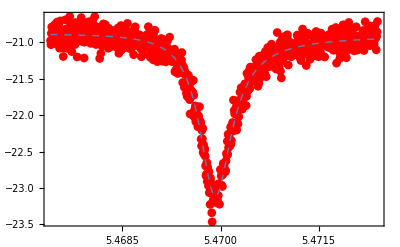

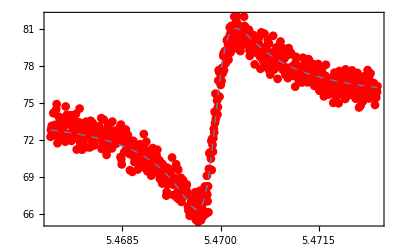

```mathematica
plotFitAmp2 = Plot[20Log[10,Abs[S21/.fitparams2[[2]]]]+groundZero-g0/.fitparams2[[2]],{f,Minf,Maxf},PlotRange->All,PlotStyle->{Dashed,Thick},LabelStyle->14];
plotFitPhase2 = Plot[180/π Arg[S21/.fitparams2[[2]]],{f,Minf,Maxf},PlotRange->All,PlotStyle->{Dashed,Thick},LabelStyle->14];
Show[plotAmp,plotFitAmp2]
Show[plotPhase,plotFitPhase2]
```

```mathematica
fittingdata=Append[fittingdata,{Pow,Qi,fr,Qα,Qe,ϕ}/.fitparams2[[2]]];
```